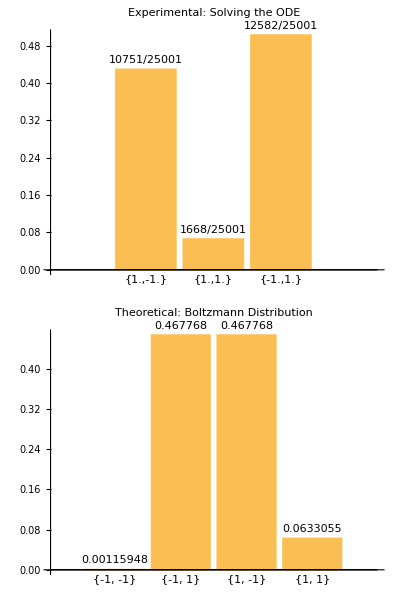

```mathematica
(*Simulating a system of 2 coupled c-bits. You can mess with parameters, with the J and h matrix etc.*)

ClearAll["Global`*"];

T=1; (*set temperature T to 1*)
tsim=50; (*set simulation duration time tsim to 50*)
h={1,1}; (*h is is a vector[1,1]*)
J={{0,-2},{-2,0}}; (*J is a 2x2 matrix with 0 on the diagonals and -2 elsewhere*)
mm={m1[t],m2[t]};
(*mm is a list of the two functions m1[t] and m2[t].These are always equal to either-1 or 1. m is the output of a c-bit.*)
xinit={-0.8,0};
(*xinit is a list of the two initial values of x1 and x2,now within the new boundary of-1 and 1*)
minit={1,-1};
(*minit is a list of the two initial values of m1 and m2,which is the c-bit output*)
z=h+J.mm;
(*z is a vector with 2 elements.The first is 1-2m2[t].The second is 1-2m1[t].*)

sol=First@NDSolve[{x1'[t]==-m1[t]+Tanh[z[[1]]/T],x2'[t]==-m2[t]+Tanh[z[[2]]/T],x1[0]==xinit[[1]],m1[0]==minit[[1]],x2[0]==xinit[[2]],m2[0]==minit[[2]],WhenEvent[x1[t]==1,m1[t]->1],WhenEvent[x1[t]==-1,m1[t]->-1],WhenEvent[x2[t]==1,m2[t]->1],WhenEvent[x2[t]==-1,m2[t]->-1]},{x1,m1,x2,m2},{t,0,tsim},DiscreteVariables->{m1,m2}];

(*First@gets the first element of the list that NDSolve returns.This would be x1[t]*)

pointsPerTimeStep=500; (*Set the number of points between t=0 and t=1,or t=1 and t=2,etc.*)
time=Range[0.,tsim,1/pointsPerTimeStep];
(*time is a list of equally spaced t values between 0 and tsim*)
m1vals=Map[m1/. sol,time];
(*m1vals is a list of the values of m1 corresponding to the t values in time*)
m2vals=Map[m2/. sol,time];
(*m2vals is a list of the values of m2 corresponding to the t values in time*)

(*Adjust index to handle new states-1 and 1*)
index=Transpose[{m1vals,m2vals}];

(*Create a histogram of the pairs*)
pairCounts=Counts[index];
keys=Keys[pairCounts];
values=Values[pairCounts];
totalCount=Total[values];
frequencies=values/totalCount;

experimentalPlot=BarChart[frequencies,ChartLabels->Placed[Map[ToString,keys,{2}],Below],LabelingFunction->(Placed[#,Above]&),PlotLabel->"Experimental: Solving the ODE"];

st={st1,st2};
(*the vector,or list st is set to st1,st2.These are new variables that have not already been defined.*)
en=-h.Transpose[st]-0.5*st.J.Transpose[st];
(*en is another new variable definition.Remember we set h to {1,1} at the beginning. en comes out to*)
Energy1={en/. {st1->-1,st2->-1},en/. {st1->-1,st2->1},en/. {st1->1,st2->-1},en/. {st1->1,st2->1}};
ptemp=Exp[-Energy1/T];
prob=1/Total[ptemp]*ptemp;

theoreticalPlot=BarChart[prob,ChartLabels->Placed[Map[ToString,{{-1,-1},{-1,1},{1,-1},{1,1}}],Below],LabelingFunction->(Placed[#,Above]&),PlotLabel->"Theoretical: Boltzmann Distribution"];

Grid[{{experimentalPlot},{theoreticalPlot}}]
```